## Data

```mathematica
Ni=50;
β=10^6;
Ci=9.61;
Di=0.16;
ηLos=10^(1/10);
ηNLos=10^(20/10);
VC=3 10^8;
fc=2.5 10^9;
No=2.0019 10^-12;
Ki=1;
B=50 10^6;
Lxti=0;
Lxts=500;
Lyti=0;
Lyts=500;
Lzti=0;
Lzts=1;
Lxs={500,1000};
Lys={500,500};
Lxi={0,500};
Lyi={0,0};
Lzi={0,0};
Lzs={1,1};
α=2;
h=80;
```

## Li and Joint

```mathematica
jointPDF3D[Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,x_,y_,z_]:=PDF[ProductDistribution[UniformDistribution[{Lxti,Lxts}],UniformDistribution[{Lyti,Lyts}],UniformDistribution[{Lzti,Lzts}]],{x,y,z}];
di[x_,xi_,y_,yi_,z_,hi_]:=Sqrt[(xi-x)^2+(yi-y)^2+(hi-z)^2];
βeta[x_,xi_,y_,yi_,z_,hi_]:=180/π ArcSin[(hi*Sqrt[(xi-x)^2+(yi-y)^2])/(di[x,xi,y,yi,z,hi] Sqrt[(xi-x)^2+(yi-y)^2+z^2])];
Plos[x_,xi_,y_,yi_,hi_,z_,Ci_,Di_]:=1/(1+Ci E^(-Di (βeta[x,xi,y,yi,z,hi]-Ci)));

Li1[x_,xi_,y_,yi_,hi_,z_,Ci_,Di_,ηLos_,ηNLos_,fc_,VC_]:=Plos[x,xi,y,yi,hi,z,Ci,Di]*((4 Pi fc)/VC)^2*di[x,xi,y,yi,z,hi]^α*ηLos+(ηNLos*(1-Plos[x,xi,y,yi,hi,z,Ci,Di])*di[x,xi,y,yi,z,hi]^α*((4 Pi fc)/VC)^2);
Mi[Ni_,Lxs_,Lys_,Lxi_,Lyi_,Lzs_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_]:= Ni* Abs[NIntegrate[jointPDF3D[Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,x,y,z],{x,Lxi,Lxs},{y,Lyi,Lys},{z,Lzi,Lzs}]];
```

## Function Objective

```mathematica
ptG3D[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,β_,B_ ,Ni_,x_,y_,z_,xi_,yi_,hi_,No_,ηLos_,ηNLos_,fc_,VC_]:=(2^((β Mi[Ni,Lxs,Lys,Lxi,Lyi,Lzs,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti])/B)-1)*No* Li1[x,xi,y,yi,z,hi,Ci,Di,ηLos,ηNLos,fc,VC]*jointPDF3D[Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,x,y,z];

ptGNint3D[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,β_,B_ ,Ni_,xi_,yi_,hi_,No_,ηLos_,ηNLos_,fc_,VC_]:=NIntegrate[ptG3D[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,β,B, Ni,x,y,z,xi,yi,hi,No,ηLos,ηNLos,fc,VC],{x,Lxi,Lxs},{y,Lyi,Lys},{z,Lzi,Lzs}];
ptTotalKiUAVs3D[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,β_,B_ ,Ni_,xi_,yi_,hi_,No_,ηLos_,ηNLos_,fc_,VC_]:=Sum[ptGNint3D[Ci,Di,Lxs[[i]],Lys[[i]],Lzs[[i]],Lxi[[i]],Lyi[[i]],Lzi[[i]],Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,β,B,Ni,xi[[All,i]],yi[[All,i]],hi,No,ηLos,ηNLos,fc,VC],{i,1,Ki}];
```

## function

```mathematica
Objetivo1[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,β_,B_ ,Ni_,xi_,yi_,hi_,No_,ηLos_,ηNLos_,fc_,VC_]:=Module[{},
xMod= ptTotalKiUAVs3D[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,β,B,Ni,xi,yi,hi,No,ηLos,ηNLos,fc,VC];
Return[xMod];
]
```

## EPSO

```mathematica
PSOE3D[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,h_,β_,B_,Ni_,No_,ηLos_,ηNLos_,fc_,VC_]:=Module[{},
iteration=3;
popSize=2000;
(*Parametrizaion of PSO*)tao=1;
tao1=0.2;
inercia1=0.5;
memorial1=2;
cooperacion1=3;
perturbacion1=0.1;
(*Límites de las variables*)Dmin={0,0,5};
Dmax={500,500,200};
(*Dmin=ConstantArray[0,3*Ki];
Dmax=ConstantArray[200,3*Ki];*)(*Dmin={0,0,0};
Dmax={200,200,200};*)D1=Length[Dmin];
xx=ConstantArray[0,{popSize,D1}];
v=ConstantArray[0,{popSize,D1}];
fitness=ConstantArray[0,popSize];
(*Posicion inicial de las particulas*)For[jj=1,jj≤D1,jj++,xx[[All,jj]]=(Dmax[[jj]]-Dmin[[jj]]) RandomReal[{0,1},popSize]+Dmin[[jj]]];
fitness=Objetivo1[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,β,B,Ni,xx[[All,1;;Ki]],xx[[All,Ki+1;;2*Ki]],h,No,ηLos,ηNLos,fc,VC];
{fgbest,indgbest}=Take[Flatten[MinimalBy[Transpose[{fitness,Range[popSize]}],First]],2];
xgbest=xx[[indgbest]];
fpbest=fitness;
xpbest=xx;
OF=ConstantArray[0,iteration];
For[count1=1,count1≤iteration,count1++,OF[[count1]]=fgbest;
inercia=inercia1+tao*RandomReal[NormalDistribution[0,1],{popSize,D1}];
inercia=Clip[inercia,{0,1}];
memoria=memorial1+tao*RandomReal[NormalDistribution[0,1],{popSize,D1}];
memoria=Clip[memoria,{0,1}];
cooperacion=cooperacion1+tao*RandomReal[NormalDistribution[0,1],{popSize,D1}];
cooperacion=Clip[cooperacion,{0,1}];
xgbest=ConstantArray[xgbest,Length[xx]];
v=inercia*v+memoria*(xpbest-xx)+cooperacion*(xgbest-xx);
xx=xx+v;
xgbest=xgbest[[1]];
For[jj=1,jj≤D1,jj++,xx[[All,jj]]=ReplacePart[xx[[All,jj]],Position[xx[[All,jj]],y_/;y<Dmin[[jj]]]->Dmin[[jj]]];
xx[[All,jj]]=ReplacePart[xx[[All,jj]],Position[xx[[All,jj]],y_/;y>Dmax[[jj]]]->Dmax[[jj]]];];
fitness=Objetivo1[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,β,B,Ni,xx[[All,1;;Ki]],xx[[All,Ki+1;;2*Ki]],h,No,ηLos,ηNLos,fc,VC];
positions=Flatten[Position[Thread[fitness<fpbest],True]];
xpbest[[positions]]=xx[[positions]];
fpbest[[positions]]=fitness[[positions]];
{fgbest,indgbest}=Take[Flatten[MinimalBy[Transpose[{fitness,Range[popSize]}],First]],2];
xgbest=Flatten[xx[[indgbest]]];
perturbacion=perturbacion1+tao1*Flatten[RandomReal[NormalDistribution[0,1],{1,Length[xgbest]}]];
perturbacion=Clip[perturbacion,{0,1}];
aux=xgbest+perturbacion;
aux={aux};
c1=Objetivo1[aux];
c2=c1[[1]];
If[fgbest>c2,xgbest=aux;
xgbest=xgbest[[1]];
fgbest=Objetivo1[aux];
fgbest=fgbest[[1]];];];
Return[fgbest];]
```

```mathematica
PSOE3D[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,h,β,B,Ni,No,ηLos,ηNLos,fc,VC]
```

0.0737561

```mathematica
AbsoluteTiming[Fig3D1=ParallelTable[{h,PSOE3D[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,h,β,B,Ni,No,ηLos,ηNLos,fc,VC]},{h,5,200,5}]]
```

{1713.29,{{5,0.0894991},{10,0.08965},{15,0.0899072},{20,0.0902724},{25,0.090745},{30,0.0913249},{35,0.0920122},{40,0.092807},{45,0.0937091},{50,0.0947186},{55,0.0958356},{60,0.0970599},{65,0.0983916},{70,0.0998308},{75,0.101377},{80,0.103031},{85,0.104792},{90,0.106661},{95,0.108637},{100,0.110721},{105,0.112912},{110,0.11521},{115,0.117616},{120,0.120129},{125,0.122749},{130,0.125477},{135,0.128312},{140,0.131255},{145,0.134305},{150,0.137463},{155,0.140728},{160,0.1441},{165,0.147579},{170,0.151166},{175,0.154861},{180,0.158663},{185,0.162572},{190,0.166588},{195,0.170713},{200,0.174944}}}

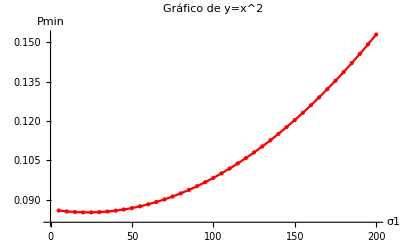

```mathematica
ListPlot[Fig3D1,Joined->True,Mesh->All,PlotStyle->Directive[Red,PointSize[Medium]],AxesLabel->{"σ1","Pmin"},PlotLabel->"Gráfico de y=x^2"]
```

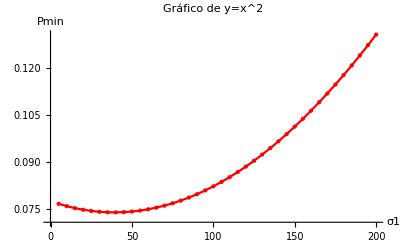

```mathematica
ListPlot[Fig3D1,Joined->True,Mesh->All,PlotStyle->Directive[Red,PointSize[Medium]],AxesLabel->{"σ1","Pmin"},PlotLabel->"Gráfico de y=x^2"]
```

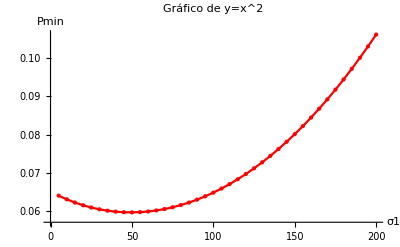

```mathematica
ListPlot[Fig3D1,Joined->True,Mesh->All,PlotStyle->Directive[Red,PointSize[Medium]],AxesLabel->{"σ1","Pmin"},PlotLabel->"Gráfico de y=x^2"]
```

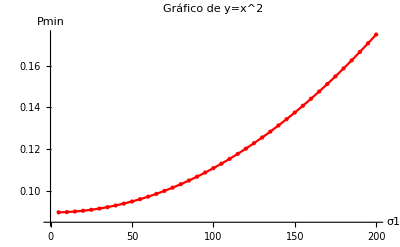

```mathematica
ListPlot[Fig3D1,Joined->True,Mesh->All,PlotStyle->Directive[Red,PointSize[Medium]],AxesLabel->{"σ1","Pmin"},PlotLabel->"Gráfico de y=x^2"]
```

```mathematica
Export["C:\\Users\\adm-wolfram\\Documents\\Resultados\\Paper-Revista\\Uniforme-EPSO-H1-V1.mat",Fig3D1];
```

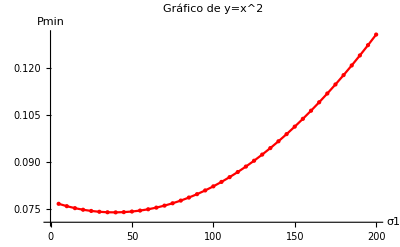

```mathematica
ListPlot[Fig3D1,Joined->True,Mesh->All,PlotStyle->Directive[Red,PointSize[Medium]],AxesLabel->{"σ1","Pmin"},PlotLabel->"Gráfico de y=x^2"]
```

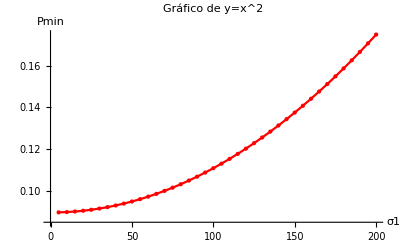

```mathematica
ListPlot[Fig3D1,Joined->True,Mesh->All,PlotStyle->Directive[Red,PointSize[Medium]],AxesLabel->{"σ1","Pmin"},PlotLabel->"Gráfico de y=x^2"]
```